```mathematica
sparseError2D[f_,n_,stepsize_]:=Module[{values,ans,i,j,coeffs},
coeffs=sparseCoefficients[f,n,2];

If[2^-n≥stepsize,
For[i=0,i≤1,i+=2^-n,
For[j=0,j≤1,j+=2^-n,
values[{i,j}]=sparseReconstruct[coeffs,{i,j},n];
]];
ans=Sqrt[stepsize^2 Sum[(f[{i,j}]-neighborAverage[values,{i,j},n])^2,{i,0,1,stepsize},{j,0,1,stepsize}]];
Return[ans]
,ans=Sqrt[stepsize^2 Sum[(f[{i,j}]-sparseReconstruct[coeffs,{i,j},n])^2,{i,0,1,stepsize},{j,0,1,stepsize}]];
Return[ans]]
]

sparseError2D2[f_,n_,stepsize_]:=Module[{values,ans,i,j,coeffs,g},
coeffs=sparseCoefficients[f,n,2];
g=sparseReconstruct[coeffs,#,n]&;
ans=Sqrt[stepsize^2 Sum[(f[{i,j}]-g[{i,j}])^2,{i,0,1,stepsize},{j,0,1,stepsize}]];
Return[ans]
]
(*This is an alternative try to make sparseError more efficient. It doesn't matter for us*)
```

```mathematica
Table[Timing[sparseError2D[Sin[Pi #[[1]]+#[[2]]]&,n,.05]][[1]],{n,1,10}]
```

{0.0562,0.070566,0.130951,0.447975,0.666677,0.868757,1.18346,1.70979,3.07829,4.91871}

```mathematica
{0.173968,0.256852,0.355101,0.515446,0.687065,0.931294,1.262521}//ListPlot
```

```mathematica
sparseError2D2[Sin[Pi #[[1]]+#[[2]]]&,4,.01]//Timing
```

{11.6458,0.0106382}

```mathematica
sparseLengths2D=Table[Length[sparseIterate[n,2]],{n,1,15}];
hierLengths2D=Table[2^n+1,{n,1,9}]^2;
```

```mathematica
Table[sparseError2D[Sin[Pi #[[1]]+#[[2]]]&,n,.05],{n,1,10}]
```

{0.15943,0.106909,0.0340714,0.0106635,0.00322183,0.000956049,0.00027648,0.0000789605,0.0000221664,6.16799×10^-6}

```mathematica
Timing[sparseError2D[Sin[Pi #[[1]]+#[[2]]]&,15,.05]]
```

{171.237,9.08449×10^-9}

```mathematica
sparse2DError={0.1594299849519286,0.1069092887971633,0.034071406916066437,0.010663486485528877,0.003221831607278467,0.0009560486161326137,0.0002764797245107613,0.00007896047401277042,0.00002216638885088263,6.167993098472236*^-6,1.6962826605317666*^-6,4.63574787834296*^-7,1.256304070465812*^-7,3.388901035042463*^-8,9.084485637964779*^-9};(*{0.15279233650074095,0.10523039169706934,0.033979928846829884,0.010638168610702218,0.0032152352583876918,0.0009442263733391095,0.0002715441207916676};*)
```

```mathematica
full2DError=Table[neighborError2D[Sin[Pi #[[1]]+#[[2]]]&,n,.01],{n,1,9}];
```

```mathematica
Table[{sparseLengths2D[n],sparseError2D[n]},{n,1,7}]
```

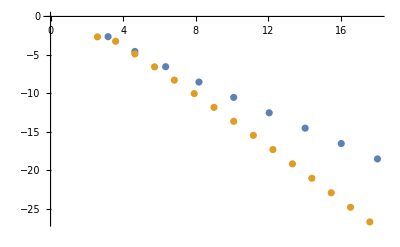

```mathematica
ListPlot[{Table[{hierLengths2D[[n]],full2DError[[n]]},{n,1,9}],Table[{sparseLengths2D[[n]],sparse2DError[[n]]},{n,1,15}]}//Log2]
```

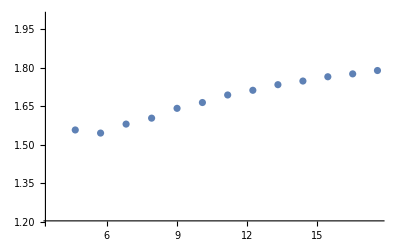

```mathematica
ListPlot[Table[{Log2[sparseLengths2D[[n]]],-(Log2[sparse2DError⟦n⟧]-Log2[sparse2DError⟦n-1⟧])/(Log2[sparseLengths2D[[n]]]-Log2[sparseLengths2D[[n-1]]])},{n,2,15}],PlotRange->{1.2,2}]
```

```mathematica
(*Rate of convergence for sparse grids at the same number of points is slowly but surely approaching 2 (definitely something >1.8)*)
```

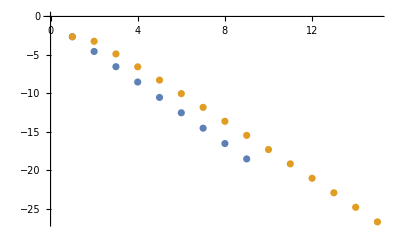

```mathematica
ListPlot[{Table[full2DError[[n]],{n,1,9}],Table[sparse2DError[[n]],{n,1,15}]}//Log2]
```

```mathematica
(*More clear that sparse(n) achieves the same general (O(1/n^2)) trend that full({n,n}) achieves*)
```